```mathematica
Graph[ReadGrof[2],VertexLabels->"Name"]//FindFullFormula
```

{v1x2x3x4x5,v14x2x3x5}

```mathematica
PaintFormula[full_,green_]:=Table[If[MemberQ[green,e],Style[e,Darker[Green]],e],{e,full}]
```

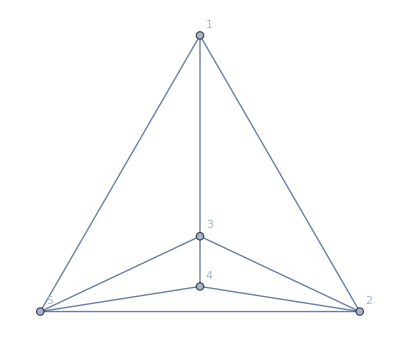
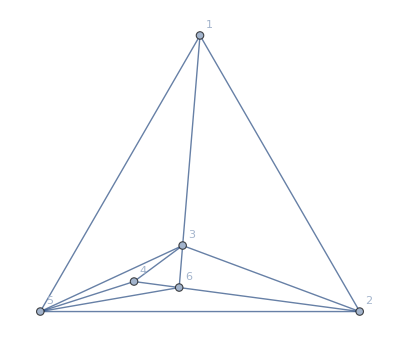
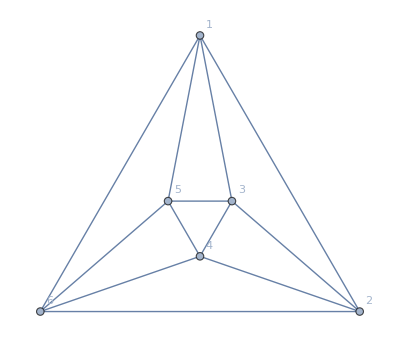
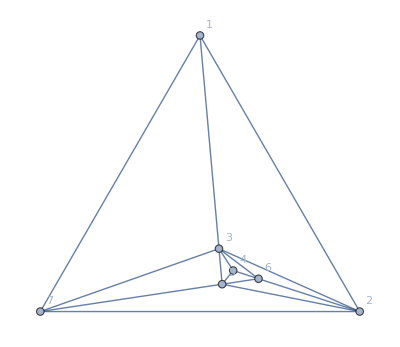
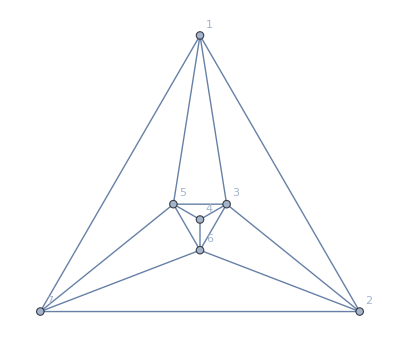
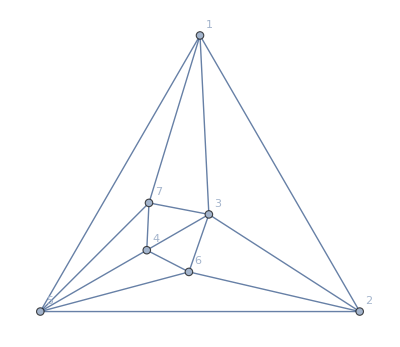
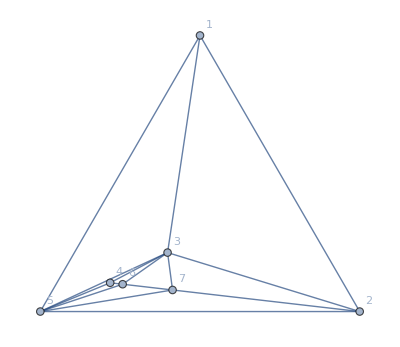
{{-Graphics-2,4<->5<->{v14x2x3x5,v1x2x3x45}
3<->5<->{v14x2x3x5,v1x2x35x4}
3<->4<->{v14x2x3x5,v1x2x34x5}
2<->5<->{v14x2x3x5,v1x25x3x4}
2<->4<->{v14x2x3x5,v1x24x3x5}
2<->3<->{v14x2x3x5,v1x23x4x5}
1<->5<->{v14x2x3x5,v15x2x3x4}
1<->3<->{v14x2x3x5,v13x2x4x5}
1<->2<->{v14x2x3x5,v12x3x4x5}},{-Graphics-3,4<->6<->{v16x24x3x5,v146x2x3x5}
4<->5<->{v16x24x3x5,v16x2x3x45}
3<->4<->{v16x24x3x5,v16x2x34x5}
2<->6<->{v16x24x3x5,v14x26x3x5}
1<->5<->{v16x24x3x5,v15x24x3x6}
1<->3<->{v16x24x3x5,v13x24x5x6}
1<->2<->{v16x24x3x5,v124x3x5x6}
5<->6<->{v16x24x3x5,v14x2x3x56,v1x24x3x56}
3<->6<->{v16x24x3x5,v14x2x36x5,v1x24x36x5}
2<->5<->{v16x24x3x5,v16x25x3x4,v14x25x3x6}
2<->3<->{v16x24x3x5,v16x23x4x5,v14x23x5x6}
3<->5<->{v16x24x3x5,v16x2x35x4,v14x2x35x6,v1x24x35x6}},{-Graphics-4,5<->6<->{v1x25x36x4,v14x2x36x5,v14x25x3x6,v14x2x3x56}
4<->6<->{v1x25x36x4,v14x2x36x5,v14x25x3x6,v1x25x3x46}
4<->5<->{v1x25x36x4,v14x2x36x5,v14x25x3x6,v1x2x36x45}
3<->5<->{v1x25x36x4,v14x2x36x5,v14x25x3x6,v14x2x35x6}
3<->4<->{v1x25x36x4,v14x2x36x5,v14x25x3x6,v1x25x34x6}
2<->6<->{v1x25x36x4,v14x2x36x5,v14x25x3x6,v14x26x3x5}
2<->4<->{v1x25x36x4,v14x2x36x5,v14x25x3x6,v1x24x36x5}
2<->3<->{v1x25x36x4,v14x2x36x5,v14x25x3x6,v14x23x5x6}
1<->6<->{v1x25x36x4,v14x2x36x5,v14x25x3x6,v16x25x3x4}
1<->5<->{v1x25x36x4,v14x2x36x5,v14x25x3x6,v15x2x36x4}
1<->3<->{v1x25x36x4,v14x2x36x5,v14x25x3x6,v13x25x4x6}
1<->2<->{v1x25x36x4,v14x2x36x5,v14x25x3x6,v12x36x4x5}},{-Graphics-5,5<->7<->{v15x24x3x67,v16x24x3x57}
4<->6<->{v15x24x3x67,v15x2x3x467}
4<->5<->{v15x24x3x67,v145x2x3x67}
3<->4<->{v15x24x3x67,v15x2x34x67}
2<->6<->{v15x24x3x67,v15x26x3x47}
1<->7<->{v15x24x3x67,v167x24x3x5}
1<->3<->{v15x24x3x67,v13x24x5x67}
1<->2<->{v15x24x3x67,v124x3x5x67}
5<->6<->{v15x24x3x67,v156x24x3x7,v156x2x3x47}
3<->7<->{v15x24x3x67,v15x24x37x6,v16x24x37x5}
3<->6<->{v15x24x3x67,v15x24x36x7,v15x2x36x47}
2<->7<->{v15x24x3x67,v15x247x3x6,v16x247x3x5}
2<->5<->{v15x24x3x67,v16x25x3x47,v14x25x3x67}
3<->5<->{v15x24x3x67,v16x24x35x7,v16x2x35x47,v14x2x35x67,v1x24x35x67}
2<->3<->{v15x24x3x67,v15x23x4x67,v15x23x47x6,v16x23x47x5,v14x23x5x67}},{-Graphics-6,6<->7<->{v14x25x37x6,v16x24x37x5,v16x25x3x47,v16x25x37x4,v14x25x3x67}
5<->7<->{v14x25x37x6,v16x24x37x5,v16x25x3x47,v16x25x37x4,v16x24x3x57}
2<->7<->{v14x25x37x6,v16x24x37x5,v16x25x3x47,v16x25x37x4,v16x247x3x5}
2<->6<->{v14x25x37x6,v16x24x37x5,v16x25x3x47,v16x25x37x4,v14x26x37x5}
2<->3<->{v14x25x37x6,v16x24x37x5,v16x25x3x47,v16x25x37x4,v16x23x47x5}
1<->7<->{v14x25x37x6,v16x24x37x5,v16x25x3x47,v16x25x37x4,v147x25x3x6}
1<->5<->{v14x25x37x6,v16x24x37x5,v16x25x3x47,v16x25x37x4,v15x24x37x6}
1<->3<->{v14x25x37x6,v16x24x37x5,v16x25x3x47,v16x25x37x4,v13x25x47x6}
1<->2<->{v14x25x37x6,v16x24x37x5,v16x25x3x47,v16x25x37x4,v124x37x5x6}
5<->6<->{v14x25x37x6,v16x24x37x5,v16x25x3x47,v16x25x37x4,v14x2x37x56,v1x24x37x56}
3<->6<->{v14x25x37x6,v16x24x37x5,v16x25x3x47,v16x25x37x4,v14x25x36x7,v1x25x36x47}
3<->5<->{v14x25x37x6,v16x24x37x5,v16x25x3x47,v16x25x37x4,v16x24x35x7,v16x2x35x47}
4<->6<->{v14x25x37x6,v16x24x37x5,v16x25x3x47,v16x25x37x4,v146x25x3x7,v146x2x37x5,v1x25x37x46}
4<->5<->{v14x25x37x6,v16x24x37x5,v16x25x3x47,v16x25x37x4,v16x245x3x7,v16x2x37x45,v1x245x37x6}
3<->4<->{v14x25x37x6,v16x24x37x5,v16x25x3x47,v16x25x37x4,v16x25x34x7,v16x2x347x5,v1x25x347x6}},{-Graphics-7,5<->7<->{v1x24x35x67,v14x2x35x67,v14x27x35x6,v16x24x35x7,v16x27x35x4,v16x24x3x57}
5<->6<->{v1x24x35x67,v14x2x35x67,v14x27x35x6,v16x24x35x7,v16x27x35x4,v14x27x3x56}
4<->5<->{v1x24x35x67,v14x2x35x67,v14x27x35x6,v16x24x35x7,v16x27x35x4,v16x27x3x45}
3<->7<->{v1x24x35x67,v14x2x35x67,v14x27x35x6,v16x24x35x7,v16x27x35x4,v16x24x37x5}
3<->6<->{v1x24x35x67,v14x2x35x67,v14x27x35x6,v16x24x35x7,v16x27x35x4,v14x27x36x5}
3<->4<->{v1x24x35x67,v14x2x35x67,v14x27x35x6,v16x24x35x7,v16x27x35x4,v16x27x34x5}
2<->5<->{v1x24x35x67,v14x2x35x67,v14x27x35x6,v16x24x35x7,v16x27x35x4,v14x25x3x67}
2<->3<->{v1x24x35x67,v14x2x35x67,v14x27x35x6,v16x24x35x7,v16x27x35x4,v14x23x5x67}
1<->5<->{v1x24x35x67,v14x2x35x67,v14x27x35x6,v16x24x35x7,v16x27x35x4,v15x24x3x67}
1<->3<->{v1x24x35x67,v14x2x35x67,v14x27x35x6,v16x24x35x7,v16x27x35x4,v13x24x5x67}
4<->7<->{v1x24x35x67,v14x2x35x67,v14x27x35x6,v16x24x35x7,v16x27x35x4,v16x247x3x5,v16x2x35x47,v1x247x35x6}
4<->6<->{v1x24x35x67,v14x2x35x67,v14x27x35x6,v16x24x35x7,v16x27x35x4,v146x27x3x5,v146x2x35x7,v1x27x35x46}
2<->6<->{v1x24x35x67,v14x2x35x67,v14x27x35x6,v16x24x35x7,v16x27x35x4,v14x267x3x5,v14x26x35x7,v1x267x35x4}
1<->7<->{v1x24x35x67,v14x2x35x67,v14x27x35x6,v16x24x35x7,v16x27x35x4,v17x24x35x6,v167x24x3x5,v167x2x35x4}
1<->2<->{v1x24x35x67,v14x2x35x67,v14x27x35x6,v16x24x35x7,v16x27x35x4,v12x35x4x67,v124x35x6x7,v124x3x5x67}},{-Graphics-8,6<->7<->{v147x26x3x5,v167x24x3x5}
4<->6<->{v147x26x3x5,v17x246x3x5}
4<->5<->{v147x26x3x5,v17x26x3x45}
3<->4<->{v147x26x3x5,v17x26x34x5}
2<->7<->{v147x26x3x5,v16x247x3x5}
1<->5<->{v147x26x3x5,v15x26x3x47}
1<->3<->{v147x26x3x5,v13x26x47x5}
1<->2<->{v147x26x3x5,v126x3x47x5}
5<->7<->{v147x26x3x5,v14x26x3x57,v16x24x3x57}
5<->6<->{v147x26x3x5,v17x24x3x56,v147x2x3x56}
3<->7<->{v147x26x3x5,v14x26x37x5,v16x24x37x5}
3<->6<->{v147x26x3x5,v17x24x36x5,v147x2x36x5}
2<->5<->{v147x26x3x5,v147x25x3x6,v16x25x3x47}
2<->3<->{v147x26x3x5,v147x23x5x6,v16x23x47x5}
3<->5<->{v147x26x3x5,v17x24x35x6,v17x26x35x4,v147x2x35x6,v14x26x35x7,v16x24x35x7,v16x2x35x47,v1x26x35x47}}}

```mathematica
Table[With[{g=Graph[ReadGrof[k],VertexLabels->"Name",GraphLayout->"TutteEmbedding",ImageSize->400]},
{Labeled[g,Style[k,Red,20]],
Sort[With[{form=FindFullFormula4[g]},
Table[e<->PaintFormula[Sort[FindFullFormula4[EdgeDelete[g,e]],MemberQ[form,#]&],form],{e,EdgeList[g]}]
],Length[#1[[2]]]<Length[#2[[2]]]&]//Column}
],{k,2,8}]
```

```mathematica
SameGraphQ[g_,h_]:=Block[{},
If[EdgeCount[g]≠EdgeCount[h],Return[False]];
If[VertexCount[g]≠VertexCount[h],Return[False]];
Fold[And,Table[EdgeQ[g,e],{e,EdgeList[h]}]]
]
```

```mathematica
SameGraphQ[WheelGraph[6],WheelGraph[5]]
```

False

```mathematica
Select[Keys[allGraphs6],SameGraphQ[allGraphs6[#,"graph"],EdgeDelete[WheelGraph[6],{1<->2}]]&]
```

{2382625}

```mathematica
allGraphs6[2382625,"colofour"]/.RepGraph6["C"]
```

-Graphics-11957506+-Graphics-11957449+-Graphics-11957425+-Graphics-11957503+-Graphics-7181041+-Graphics-7181095+-Graphics-7176643+-Graphics-7174537+-Graphics-7176667+-Graphics-11957422+-Graphics-7181014+-Graphics-7174456+-Graphics-7174480+-Graphics-7176640+-Graphics-7174534+-Graphics-7174453